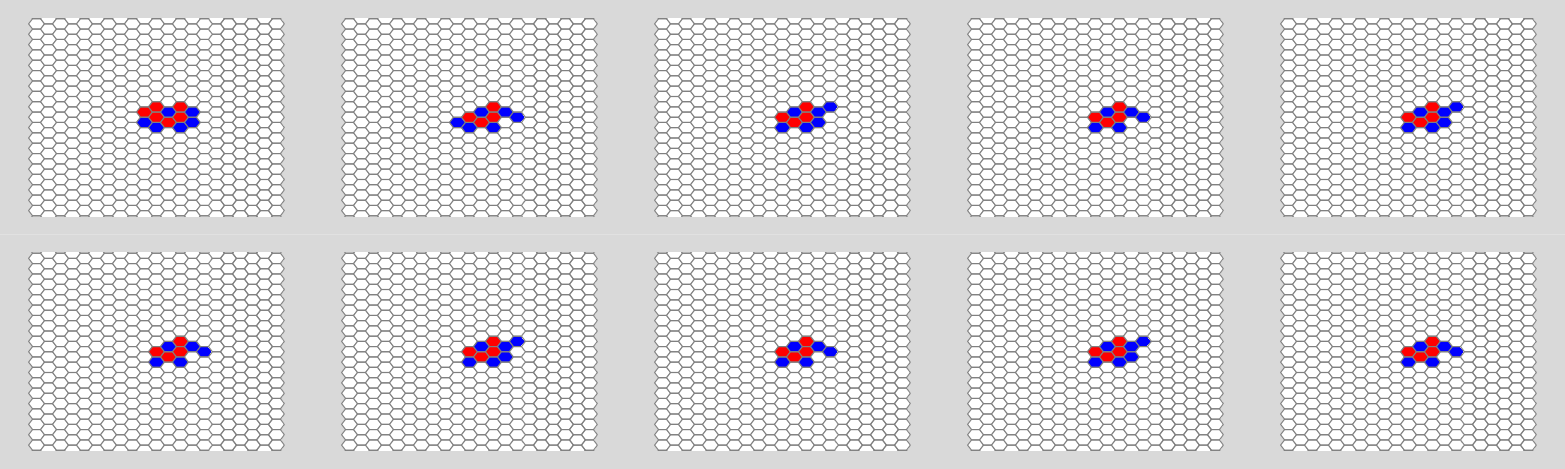

```mathematica
(*GRID PARAMETERS*)
size=10;  (*Number of hexagons along one side of the grid*)
cellRadius=0.5;  (*Radius of each hexagon cell*)

(*Function to create a hexagon centered at {x,y} with given radius*)
hexagon[{x_,y_},radius_]:=Polygon[Table[{x+radius Cos[theta],y+radius Sin[theta]},{theta,0,2 Pi,Pi/3}]];

(*Generate coordinates for hexagonal grid*)
hexagonCoordinates=Flatten[Table[{3/2 i cellRadius,Sqrt[3] (j+0.5 Mod[i,2]) cellRadius},{i,-size,size},{j,-size,size}],1];

(*Initialize all states to 0*)
initialStates=AssociationThread[hexagonCoordinates->ConstantArray[0,Length[hexagonCoordinates]]];

(*pre-set states, for testing purposes*)

(*CENTER CELL*)
initialStates[{0.0,0.0}]=1; 

(*UPPER/LOWER*)
initialStates[{0.0,0.0+Sqrt[3]/2}]=1;
initialStates[{0.0,0.0-Sqrt[3]/2}]=2; 

(*RIGHT,UPPER/LOWER*)
initialStates[{0.75,0.0-Sqrt[3]/4}]=1; 
initialStates[{0.75,0.0+Sqrt[3]/4}]=2;

(*LEFT,UPPER/LOWER*)
initialStates[{-0.75,0.0+Sqrt[3]/4}]=1; 
initialStates[{-0.75,0.0-Sqrt[3]/4}]=2; 

(*--------------------------------------*)

(*CENTER CELL*)
initialStates[{1.5,0.0}]=1; 

(*UPPER/LOWER*)
initialStates[{1.5,0.0+Sqrt[3]/2}]=1;
initialStates[{1.5,0.0-Sqrt[3]/2}]=2; 

(*RIGHT,UPPER/LOWER*)
initialStates[{2.25,0.0-Sqrt[3]/4}]=2; 
initialStates[{2.25,0.0+Sqrt[3]/4}]=2;

(*LEFT,UPPER/LOWER*)
initialStates[{-1.5,0.0+Sqrt[3]/4}]=1; 
initialStates[{-1.5,0.0-Sqrt[3]/4}]=2; 

(*Function to get neighbors of a hexagon at {x,y}*)
getNeighbors[{x_,y_}]:={
{x,y+Sqrt[3]/2},{x,y-Sqrt[3]/2},
{x+0.75,y+Sqrt[3]/4},{x+0.75,y-Sqrt[3]/4},
{x-0.75,y+Sqrt[3]/4},{x-0.75,y-Sqrt[3]/4}};

(*Function to update states based on neighbor states*)
updateStates[states_]:=Module[{prop1=1,prop2=1,surv1=1,surv2=1,neighbors,newState,count1,count2,count0},(*Initialize newState as a copy of the current states*)newState=Association[states];
Do[
neighbors=getNeighbors[hexagonCoordinates[[i]]];
count1=0;
count2=0;
count0=0;
(*Count neighbor states*)Do[If[KeyExistsQ[states,neighbors[[j]]],Switch[states[neighbors[[j]]],1,count1+=1,2,count2+=1,0,count0+=1]],{j,Length[neighbors]}];
(*Update the state based on the neighbor counts and rules*)If[states[hexagonCoordinates[[i]]]==0,If[count1>count2&&count1>prop1,newState[hexagonCoordinates[[i]]]=1,If[count2>count1&&count2>prop2,newState[hexagonCoordinates[[i]]]=2,newState[hexagonCoordinates[[i]]]=0]],If[states[hexagonCoordinates[[i]]]==1,If[count2>surv1,newState[hexagonCoordinates[[i]]]=1,newState[hexagonCoordinates[[i]]]=0],If[count1>surv2,newState[hexagonCoordinates[[i]]]=2,newState[hexagonCoordinates[[i]]]=0]]],{i,Length[hexagonCoordinates]}];
Return[newState]]


(*Create a list to store states after each update*) 
stateHistory={initialStates};

(*Loop through 10 state updates*)
Do[newStates=updateStates[stateHistory[[-1]]];
AppendTo[stateHistory,newStates]; ,
{n,10} ];

(*Function to display the hexagonal grid*)
displayHexagonalGrid[states_]:=
Graphics[Table[{If[states[coord]==1,Red,
If[states[coord]==2,Blue,White]],
EdgeForm[Gray],hexagon[coord,cellRadius]},
{coord,hexagonCoordinates}],
PlotRange->{{-size,size}*cellRadius*1.6,
{-size,size}*cellRadius*1.6},
Background->LightGray];

(*number of columns for displaying different states*)
columns=5;
gridGraphics=Table[displayHexagonalGrid[stateHistory[[i]]],
{i,Length[stateHistory]}];

(*grid layout for display*)
Grid[Partition[gridGraphics,columns],Spacings->{1,1}]
```